Datasets

Especially in larger organizations, computing often centers around dealing with large amounts of structured data. The Wolfram Language has a very powerful way to deal with structured data, using what it calls datasets.

A simple example of a dataset is formed from an association of associations.

Create a simple dataset that can be viewed as having 2 rows and 3 columns:

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

Dataset[<>]

The Wolfram Language displays most datasets in tabular form. You can extract parts from datasets just like you would from associations.

Get the element from “row b” and “column z”:

```mathematica
data["b","z"]
```

7

You can first extract the whole “b row”, then get the “z” element of the result:

```mathematica
data["b"]["z"]
```

7

You can also just get the whole “b row” of the dataset. The result is a new dataset, which for ease of reading happens to be displayed in this case as a column.

Generate a new dataset from the “b row” of the original dataset:

```mathematica
data["b"]
```

Dataset[<>]

Here is the dataset that corresponds to the “z column” for all “rows”.

Generate a dataset consisting of the “z column” for all rows:

```mathematica
data[All,"z"]
```

Dataset[<>]

Extracting parts of datasets is just the beginning. Anywhere you can ask for a part you can also give a function that will be applied to all parts at that level.

Get totals for each row by applying Total to all columns for all the rows:

```mathematica
data[All,Total]
```

Dataset[<>]

If we use f instead of Total, we can see what’s going on: the function is being applied to each of the “row” associations.

Apply the function f to each row:

```mathematica
data[All,f]
```

Dataset[<>]

Apply a function that adds the x and z elements of each association:

```mathematica
data[All,#x+#z&]
```

Dataset[<>]

You can use any function; here’s PieChart:

```mathematica
data[All,PieChart]
```

Dataset[<>]

You can give a function to apply to all rows too.

This extracts the value of each “z column”, then applies f to the association of results:

```mathematica
data[f,"z"]
```

f[<|a→3,b→7|>]

Apply f to the totals of all columns:

```mathematica
data[f,Total]
```

f[<|a→6,b→22|>]

Find the maximum of these totals:

```mathematica
data[Max,Total]
```

22

You can always “chain” queries, for example first finding the totals for all rows, then picking out the result for the “b row”.

Find totals for all rows, then pick out the total for the “b row”:

```mathematica
data[All,Total]["b"]
```

22

It’s equivalent to this:

```mathematica
data["b",Total]
```

22

Particularly when one’s dealing with large datasets, it’s common to want to select parts based on a criterion. The operator form of Select provides a very convenient way to do this.

Select numbers greater than 5 from a list:

```mathematica
Select[{1,3,6,8,2,5,9,7},#>5&]
```

{6,8,9,7}

Another way to get the same answer, using the operator form of Select:

```mathematica
Select[#>5&][{1,3,6,8,2,5,9,7}]
```

{6,8,9,7}

The operator form of Select is a function which can be applied to actually perform the Select operation.

Make a dataset by selecting only rows whose “z column” is greater than 5:

```mathematica
data[Select[#z>5&]]
```

Dataset[<>]

For each row, select columns whose values are greater than 5, leaving a ragged structure:

```mathematica
data[All,Select[#>5&]]
```

Dataset[<>]

Normal turns the dataset into an ordinary association of associations:

```mathematica
Normal[%]
```

<|a→<||>,b→<|y→10,z→7|>|>

Many Wolfram Language functions have operator forms.

Sort according to the values of a function applied to each element:

```mathematica
SortBy[{1,3,6,8,2,5,9,7},If[EvenQ[#],#,10+#]&]
```

{2,6,8,1,3,5,7,9}

SortBy has an operator form:

```mathematica
SortBy[If[EvenQ[#],#,10+#]&][{1,3,6,8,2,5,9,7}]
```

{2,6,8,1,3,5,7,9}

Sort rows according to the value of the difference of the x and y columns:

```mathematica
data[SortBy[#x-#y&]]
```

Dataset[<>]

Sort the rows, and find the total of all columns:

```mathematica
data[SortBy[#x-#y&],Total]
```

Dataset[<>]

Sometimes you want to apply a function to each element in the dataset.

Apply f to each element in the dataset:

```mathematica
data[All,All,f]
```

Dataset[<>]

Sort the rows before totaling the squares of their elements:

```mathematica
data[SortBy[#x-#y&],Total,#^2&]
```

Dataset[<>]

Datasets can contain arbitrary mixtures of lists and associations. Here’s a dataset that can be thought of as a list of records with named fields.

A dataset formed from a list of associations:

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

Dataset[<>]

It’s OK for entries to be missing:

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7|>}]
```

Dataset[<>]

Now that we’ve seen some simple examples, it’s time to look at something slightly more realistic. Let’s import a dataset giving properties of planets and moons. The dataset has a hierarchical structure, with each planet having a mass and radius of its own, and then also having a collection of moons, each of which have their own properties. This general structure is extremely common in practice (think students and grades, customers and orders, etc.).

Get a hierarchical dataset of planets and moons from the cloud:

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

Dataset[<>]

Find the radii of all the planets:

```mathematica
planets[All,"Radius"]
```

Dataset[<>]

Make a bar chart of planet radii:

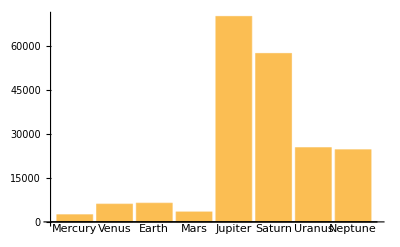

```mathematica
BarChart[planets[All,"Radius"],ChartLabels->Automatic]
```

If we ask about the moons of Mars, we get a dataset, which we can then query further.

Get a dataset about the moons of Mars:

```mathematica
planets["Mars","Moons"]
```

Dataset[<>]

“Drill down” to make a table of radii of all the moons of Mars:

```mathematica
planets["Mars","Moons",All,"Radius"]
```

Dataset[<>]

We can do computations about the moons of all planets. First, let’s just find out how many moons are listed for each planet.

Make a dataset of the number of moons listed for each planet:

```mathematica
planets[All,"Moons",Length]
```

Dataset[<>]

Find the total mass of all moons for each planet:

```mathematica
planets[All,"Moons",Total,"Mass"]
```

Dataset[<>]

Get the same result, but only for planets with more than 10 moons:

```mathematica
planets[Select[Length[#Moons]>10&],"Moons",Total,"Mass"]
```

Dataset[<>]

Make a pie chart of the result:

```mathematica
PieChart[%,ChartLegends->Automatic]
```

-Graphics-

Get a dataset with moons that are more than 1% of the mass of the Earth.

For all moons, select ones whose mass is greater than 0.01 times the mass of the Earth:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]]
```

Dataset[<>]

Get the list of keys (i.e. moon names) in the resulting association for each planet:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][All,Keys]
```

Dataset[<>]

Get the underlying association:

```mathematica
Normal[%]
```

<|Mercury→{},Venus→{},Earth→{Moon},Mars→{},Jupiter→{Callisto,Ganymede,Io},Saturn→{Titan},Uranus→{},Neptune→{}|>

Join together, or “catenate”, the lists for all keys:

```mathematica
Catenate[%]
```

{Moon,Callisto,Ganymede,Io,Titan}

Here’s the whole computation in one line:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][Catenate,Keys]//Normal
```

{Moon,Callisto,Ganymede,Io,Titan}

Here’s one more example, where we find the logarithm of the mass of each moon, then make a number line plot of these values for each planet.

Make number line plots of the logarithms of masses for moons of each planet:

```mathematica
planets[All,"Moons",NumberLinePlot[Values[#]]&,Log[#Mass/LinguisticAssistant]&]
```

Dataset[<>]

As a final example, let’s make a word cloud of names of moons, sized according to the masses of the moons. To do this, we need a single association that associates the name of each moon with its mass.

When given an association, WordCloud determines sizes from values in the association:

```mathematica
WordCloud[<|"A"->5,"B"->4,"C"->3,"D"->2,"E"->1|>]
```

-Graphics-

The function Association combines associations:

```mathematica
Association[<|"a"->1,"b"->2|>,<|"c"->3|>]
```

<|a→1,b→2,c→3|>

Generate the word cloud of moon masses:

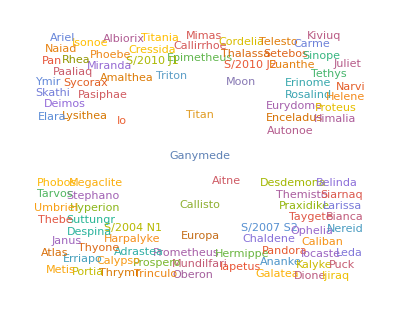

```mathematica
planets[WordCloud[Association[Values[#]]]&,"Moons",All,"Mass"]
```

For what it does, the code here is surprisingly simple. But we can make it slightly more streamlined by using @* or /*.

We’ve seen before that we can write something like f[g[x]] as f@g@x or x//g//f. We can also write it f[g[#]]&[x]. But what about f[g[#]]&? Is there a short way to write this? The answer is that there is, in terms of the function composition operators @* and /*.

f@*g@*h represents a composition of functions to be applied right-to-left:

```mathematica
(f@*g@*h)[x]
```

f[g[h[x]]]

h/*g/*f represents a composition of functions to be applied left-to-right:

```mathematica
(h/*g/*f)[x]
```

f[g[h[x]]]

Here’s the previous code rewritten using composition @*:

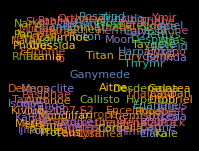

```mathematica
planets[WordCloud@*Association@*Values,"Moons",All,"Mass"]
```

And using right composition /*:

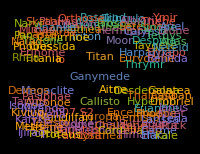

```mathematica
planets[Values/*Association/*WordCloud,"Moons",All,"Mass"]
```

As a final example, let’s look at another dataset—this time coming straight from the Wolfram Data Repository. Here’s a webpage (about big meteors) from the repository:

-Graphics-

To get the main dataset that’s mentioned here, just use ResourceData.

Get the dataset just by giving its name to ResourceData:

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

Dataset[<>]

Extract the coordinates entry from each row, and plot the results:

```mathematica
GeoListPlot[fireballs[All,"Coordinates"]]
```

-Graphics-

Make a histogram of the altitudes:

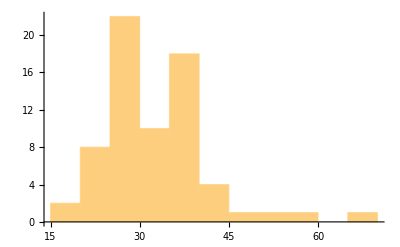

```mathematica
Histogram[fireballs[All,"Altitude"]]
```

Vocabulary

Dataset[data] |   | a dataset
Normal[dataset] |   | convert a dataset to normal lists and associations
Catenate[{assoc_1, ...}] |   | catenate associations, combining their elements
f@*g |   | composition of functions (f[g[x]] when applied to x)
f/*g |   | right composition (g[f[x]] when applied to x)

"13 Exercises Available" | "Get Started »"

Note: These exercises use the dataset planets=CloudGet["http: // wolfr.am/7FxLgPm5"].

Make a word cloud of the planets, with weights determined by their number of moons. »

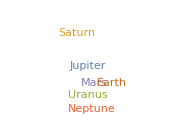
| Expected output: |  
  | -Graphics- |

Make a bar chart of the number of moons for each planet. »

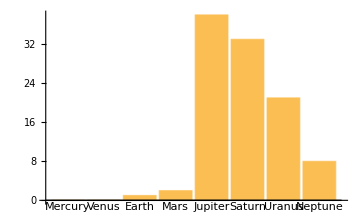
| Expected output: |  
  | -Graphics- |

Make a dataset of the masses of the planets, sorted by their number of moons. »

| Expected output: |  
  | Dataset[<>] |

Make a dataset of planets and the mass of each one’s most massive moon. »

| Expected output: |  
  | Dataset[<>] |

Make a dataset of masses of planets, where the planets are sorted by the largest mass of their moons. »

| Expected output: |  
  | Dataset[<>] |

Make a dataset of the median mass of all moons for each planet. »

| Expected output: |  
  | Dataset[<>] |

For each planet, make a list of moons larger in mass than 0.0001 Earth masses. »

| Expected output: |  
  | Dataset[<>] |

Make a word cloud of countries in Central America, with the names of countries proportional to the lengths of the Wikipedia article about them. »

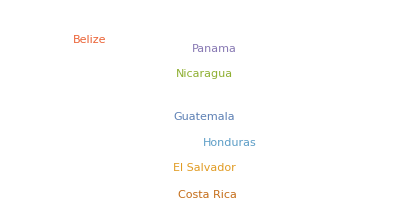
| Sample expected output: |  
  | -Graphics- |

Find the maximum observed altitude in the Fireballs & Bolides dataset. »

| Expected output: |  
  | 66.6 "km" |

Find a dataset of the 5 largest observed altitudes in the Fireballs & Bolides dataset. »

| Expected output: |  
  | Dataset[<>] |

Make a histogram of the differences in successive peak brightness times in the Fireballs & Bolides dataset. »

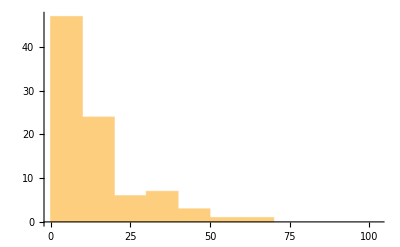
| Expected output: |  
  | -Graphics- |

Plot the nearest cities for the first 10 entries in the Fireballs & Bolides dataset, labeling each city. »

| Expected output: |  
  | -Graphics- |

Plot the nearest cities for the 10 entries with largest altitudes in the Fireballs & Bolides dataset, labeling each city. »

| Expected output: |  
  | -Graphics- |

Q&A

What kinds of data can datasets contain?

Any kinds. Not just numbers and text but also images, graphs and lots more. There’s no need for all elements of a particular row or column to be the same type.

Can I turn spreadsheets into datasets?

Yes. SemanticImport is often a good way to do it.

What are databases and how do they relate to Dataset?

Databases are a traditional way to store structured data in a computer system. Databases are often set up to allow both reading and writing of data. Dataset is a way to represent data that might be stored in a database so that it’s easy to manipulate with the Wolfram Language.

How does data in Dataset compare to data in an SQL (relational) database?

SQL databases are strictly based on tables of data arranged in rows and columns of particular types, with additional data linked in through “foreign keys”. Dataset can have any mixture of types of data, with any number of levels of nesting, and any hierarchical structure, somewhat more analogous to a NoSQL database, but with additional operations made possible by the symbolic nature of the language.

Can I use datasets to set up entities and values for them?

Yes. If you’ve got a dataset that’s an association of associations, with the outer keys being entities and the inner ones being properties, then you just have to put this inside EntityStore, and you’ll pretty much have everything set up.

Tech Notes

Dataset supports a new kind of symbolic database structure which generalizes both relational and hierarchical databases.

Dataset has many additional mechanisms and capabilities that we haven’t discussed.

Everything that can be done with queries on datasets can also be done by using functions like Map and Apply on underlying lists and association—but it’s typically much simpler with dataset queries.

You can connect the Wolfram Language directly to SQL databases—and do queries with SQL syntax—using DatabaseLink.

More to Explore

Guide to Computation with Structured Datasets in the Wolfram Language »